# Define point force Kelvin solutions

First we define the point source Greens functions

```mathematica
x = xo - xs;
y = yo - ys;
C0 = 1/ (4 * Pi *(1-ν));
r = Sqrt[x^2 + y^2];
g = -C0 * Log[r];
gx = -C0*x/r^2;
gy = -C0*y/r^2;
gxy = 2*C0*x*y/r^4;
gxx = C0*(x^2 - y^2)/r^4;
gyy = -gxx;
ux = fx/(2*μ)*((3-4*ν)*g - x*gx) + fy/(2*μ)*(-y*gx) ;
uy = fx/(2*μ)*(-x*gy) + fy/(2*μ)*((3-4*ν)*g -y*gy);
sxx = fx*(2*(1 - ν)*gx - x*gxx) + fy*(2*ν* gy - y*gxx)
syy = fx*(2*ν*gx - x*gyy) + fy * (2*(1 - ν)*gy - y*gyy)
sxy = fx*((1 - 2*ν)*gy - x*gxy) + fy*((1 - 2*ν)*gx - y*gxy)
```

fx (-(xo-xs)/(2 π ((xo-xs)^2+(yo-ys)^2))-((xo-xs) ((xo-xs)^2-(yo-ys)^2))/(4 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν)))+fy (-(((xo-xs)^2-(yo-ys)^2) (yo-ys))/(4 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν))-((yo-ys) ν)/(2 π ((xo-xs)^2+(yo-ys)^2) (1-ν)))

fy (-(yo-ys)/(2 π ((xo-xs)^2+(yo-ys)^2))+(((xo-xs)^2-(yo-ys)^2) (yo-ys))/(4 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν)))+fx (((xo-xs) ((xo-xs)^2-(yo-ys)^2))/(4 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν))-((xo-xs) ν)/(2 π ((xo-xs)^2+(yo-ys)^2) (1-ν)))

fy (-((xo-xs) (yo-ys)^2)/(2 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν))-((xo-xs) (1-2 ν))/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν)))+fx (-((xo-xs)^2 (yo-ys))/(2 π ((xo-xs)^2+(yo-ys)^2)^2 (1-ν))-((yo-ys) (1-2 ν))/(4 π ((xo-xs)^2+(yo-ys)^2) (1-ν)))

## Integrate point sources over a line (solutions same as Crouch & Starfield, 1983)

The source is defined as a line . We evaluate these stress component solutions only along the nodal line i.e., .
Note that the stress components evaluated along the nodal line are non-zero for 1 component of force/traction while they are 0 for the other!

```mathematica
sxymod = ReplaceAll[sxy,{ys->0,yo->0}];
sxyint = Re[Integrate[sxymod,{xs,-1,1},Assumptions->{Im[xo]==0,-1<=Re[xo]<=1} ]]

sxxmod = ReplaceAll[sxx,{ys->0,yo->0}];
sxxint = Re[Integrate[sxxmod,{xs,-1,1},Assumptions->{Im[xo]==0,-1<=Re[xo]<=1} ]]

syymod = ReplaceAll[syy,{ys->0,yo->0}];
syyint = Re[Integrate[syymod,{xs,-1,1},Assumptions->{Im[xo]==0,-1<=Re[xo]<=1} ]]
```

Re[((fy-2 fy ν) ArcCoth[xo])/(-1+ν)]/(2 π)

Re[(fx (3-2 ν) ArcCoth[xo])/(-1+ν)]/(2 π)

Re[(fx (-1+2 ν) ArcCoth[xo])/(-1+ν)]/(2 π)

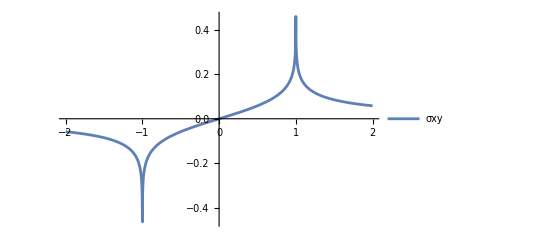

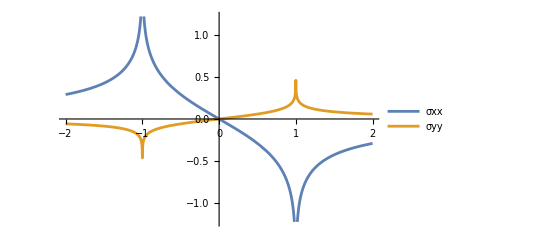

```mathematica
Plot[ReplaceAll[sxyint,{fx -> 1,fy->-1, μ->1,ν->0.25}],{xo,-2,2},PlotLegends->{"σxy"}]
Plot[{ReplaceAll[sxxint,{fx -> 1,fy->1, μ->1,ν->0.25}],ReplaceAll[syyint,{fx -> 1,fy->1, μ->1,ν->0.25}]},{xo,-2,2},PlotLegends->{"σxx","σyy"}]
```

# Integrate point source over a line

Here we derive the more general solutions over the entire full space

```mathematica
SXYindef = Integrate[sxy,xs,GeneratedParameters->C];
SXYdef = ReplaceAll[SXYindef,{xs->1}]-ReplaceAll[SXYindef,{xs->-1}]//FullSimplify

SXXindef = Integrate[sxx,xs,GeneratedParameters->C];
SXXdef = ReplaceAll[SXXindef,{xs->1}]-ReplaceAll[SXXindef,{xs->-1}]//FullSimplify

SYYindef = Integrate[syy,xs,GeneratedParameters->C];
SYYdef = ReplaceAll[SYYindef,{xs->1}]-ReplaceAll[SYYindef,{xs->-1}]//FullSimplify
```

-((2 (yo-ys) (fx (1-xo^2+(yo-ys)^2)+2 fy xo (-yo+ys)))/((1+(-2+xo) xo+(yo-ys)^2) (1+xo (2+xo)+(yo-ys)^2))-2 fx (-1+ν) ArcTan[(-1+xo)/(yo-ys)]+2 fx (-1+ν) ArcTan[(1+xo)/(yo-ys)]+1/2 fy (-1+2 ν) (-Log[1+(-2+xo) xo+(yo-ys)^2]+Log[1+xo (2+xo)+(yo-ys)^2]))/(4 π (-1+ν))

(-(2 (fy (1-xo^2+(yo-ys)^2)+2 fx xo (yo-ys)) (yo-ys))/((1+(-2+xo) xo+(yo-ys)^2) (1+xo (2+xo)+(yo-ys)^2))+2 fy ν ArcTan[(yo-ys)/(-1+xo)]-2 fy ν ArcTan[(yo-ys)/(1+xo)]+1/2 fx (-3+2 ν) (Log[1+(-2+xo) xo+(yo-ys)^2]-Log[1+xo (2+xo)+(yo-ys)^2]))/(4 π (-1+ν))

((2 (fy (1-xo^2+(yo-ys)^2)+2 fx xo (yo-ys)) (yo-ys))/((1+(-2+xo) xo+(yo-ys)^2) (1+xo (2+xo)+(yo-ys)^2))+2 fy (-1+ν) ArcTan[(-1+xo)/(yo-ys)]-2 fy (-1+ν) ArcTan[(1+xo)/(yo-ys)]-1/2 fx (-1+2 ν) (Log[1+(-2+xo) xo+(yo-ys)^2]-Log[1+xo (2+xo)+(yo-ys)^2]))/(4 π (-1+ν))

## Plot stress components for f_x = 1, f_y = 0

The components  contain logarithmic singularities, while is discontinuous but non-singular. In the plot below, I plot each of the stress components at y = 0, which is where the source exists . The plot for  appears that way because the discontinuity is exactly on the source; shifting the observation location infinitesimally in the y-direction shows a Heaviside function instead.

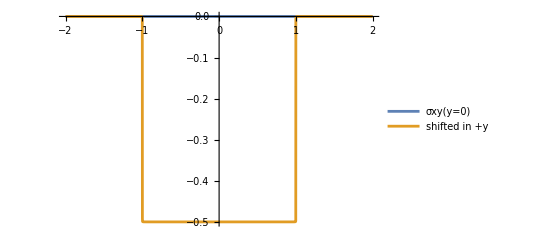

```mathematica
Plot[{ReplaceAll[sxyint,{fx -> 1,fy->0, μ->1,ν->0.25}],
ReplaceAll[SXYdef,{fx->1,fy->-0,μ->1,ν->0.25,yo->0.00001,ys->0}]},
{xo,-2,2},PlotLegends->{"σxy(y=0)","shifted in +y"}]
```

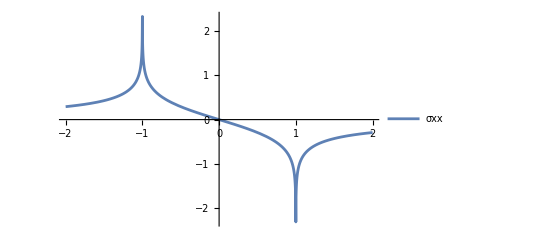

```mathematica
Plot[ReplaceAll[sxxint,{fx -> 1,fy->0, μ->1,ν->0.25}],{xo,-2,2},PlotLegends->{"σxx"}]
```

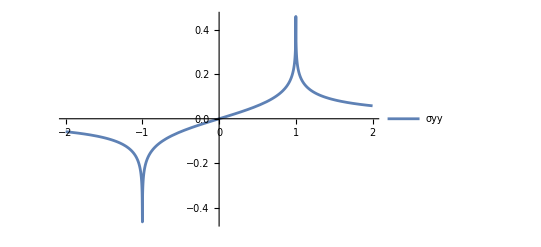

```mathematica
Plot[ReplaceAll[syyint,{fx -> 1,fy->0, μ->1,ν->0.25}],{xo,-2,2},PlotLegends->{"σyy"}]
```

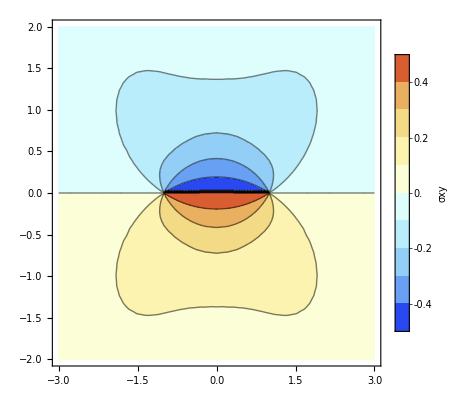
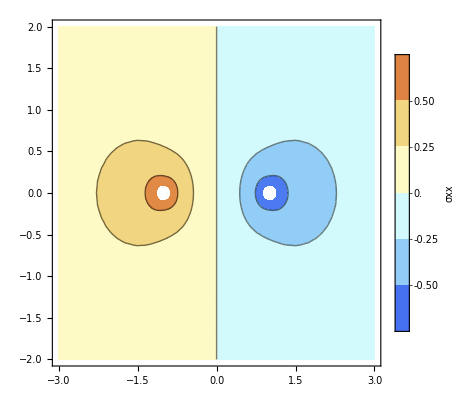
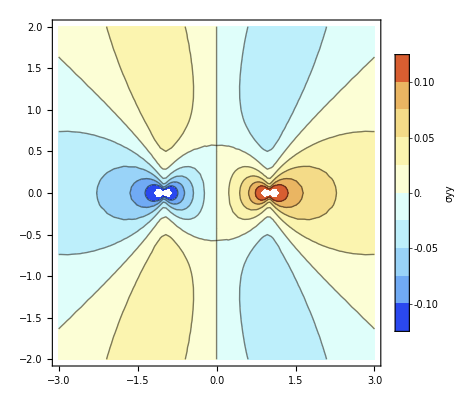

```mathematica
{ContourPlot[ReplaceAll[SXYdef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σxy"],ColorFunction->"LightTemperatureMap"],
ContourPlot[ReplaceAll[SXXdef,{fx->1,fy->-0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σxx"],ColorFunction->"LightTemperatureMap"],
ContourPlot[ReplaceAll[SYYdef,{fx->1,fy->0,μ->1,ν->0.25,ys->0}],{xo,-3,3},{yo,-2,2},PlotLegends->BarLegend[Automatic,LegendLabel->"σyy"],ColorFunction->"LightTemperatureMap"]}
```

## Integrate stress components assuming f_y = 0 and look for the order of singularity

```mathematica
SXY0 = ReplaceAll[SXYindef,{xs->1,fy->0,ys->0}]-ReplaceAll[SXYindef,{xs->-1,fy->0,ys->0}]//FullSimplify
SXX0= ReplaceAll[SXXindef,{xs->1,fy->0,yo-ys->0}]-ReplaceAll[SXXindef,{xs->-1,fy->0,yo-ys->0}]//FullSimplify

SYYindef0 = Integrate[ReplaceAll[syy,{yo->0,ys->0}],xs,GeneratedParameters->C];
SYY0 = ReplaceAll[SYYindef0,{xs->1,fy->0}]-ReplaceAll[SYYindef0,{xs->-1,fy->0}]//FullSimplify
```

(fx (((-1+xo) yo)/((-1+xo)^2+yo^2)-((1+xo) yo)/((1+xo)^2+yo^2)+2 (-1+ν) ArcTan[(-1+xo)/yo]-2 (-1+ν) ArcTan[(1+xo)/yo]))/(4 π (-1+ν))

(fx (-3+2 ν) (Log[(-1+xo)^2]-Log[(1+xo)^2]))/(8 π (-1+ν))

-(fx (-1+2 ν) (Log[-1+xo]-Log[1+xo]))/(4 π (-1+ν))

# Integrate point source over a 2-d rectangle

The procedure is straightforward for 2-d sources. First double integrate the point source solutions as indefinite integrals, then evaluate them at the four corners of the rectangle. Looking at the resulting expressions for the stress components, one can guess that the singularities disappear because the pre-factor to the logarithmic terms is of the form , for which we know  because the coefficient grows and shrinks much faster than the  term does! 

The trouble with these solutions however, is that the appearance of ArcTan functions means that there a whole lot of silly issues that appear because of the branch cut properties of ArcTan. One way to resolve these issues is to patiently and painstakingly combine similar terms using the following property:



Following this, use the ArcTan[x,y] formula instead of ArcTan[y/x]

```mathematica
SXYindef = Integrate[sxy,xs,ys,GeneratedParameters->C];
SXXindef = Integrate[sxx,xs,ys,GeneratedParameters->C];
SYYindef = Integrate[syy,xs,ys,GeneratedParameters->C];

SXY2d = ReplaceAll[SXYindef,{xs->a,ys->b,fy->0}]-
ReplaceAll[SXYindef,{xs->a,ys->-b,fy->0}]-
ReplaceAll[SXYindef,{xs->-a,ys->b,fy->0}]+
ReplaceAll[SXYindef,{xs->-a,ys->-b,fy->0}]//FullSimplify
SXX2d= ReplaceAll[SXXindef,{xs->a,ys->b,fy->0}]-
ReplaceAll[SXXindef,{xs->a,ys->-b,fy->0}]-
ReplaceAll[SXXindef,{xs->-a,ys->b,fy->0}]+
ReplaceAll[SXXindef,{xs->-a,ys->-b,fy->0}]//FullSimplify
SYY2d= ReplaceAll[SYYindef,{xs->a,ys->b,fy->0}]-
ReplaceAll[SYYindef,{xs->a,ys->-b,fy->0}]-
ReplaceAll[SYYindef,{xs->-a,ys->b,fy->0}]+
ReplaceAll[SYYindef,{xs->-a,ys->-b,fy->0}]//FullSimplify
```

1/(8 π (-1+ν))fx (2 (b-yo) (-1+2 ν) ArcTan[(a-xo)/(b-yo)]+2 (b-yo) ArcTan[(b-yo)/(a-xo)]+2 (b-yo) ArcTan[(b-yo)/(a+xo)]+2 (-b+yo) (-1+2 ν) ArcTan[(a+xo)/(-b+yo)]+2 (b+yo) (-1+2 ν) ArcTan[(-a+xo)/(b+yo)]-2 (b+yo) (-1+2 ν) ArcTan[(a+xo)/(b+yo)]+2 (b+yo) ArcTan[(b+yo)/(-a+xo)]-2 (b+yo) ArcTan[(b+yo)/(a+xo)]-a Log[(a-xo)^2+(b-yo)^2]+xo Log[(a-xo)^2+(b-yo)^2]+2 a ν Log[(a-xo)^2+(b-yo)^2]-2 xo ν Log[(a-xo)^2+(b-yo)^2]-a Log[(a+xo)^2+(b-yo)^2]-xo Log[(a+xo)^2+(b-yo)^2]+2 a ν Log[(a+xo)^2+(b-yo)^2]+2 xo ν Log[(a+xo)^2+(b-yo)^2]+a Log[(a-xo)^2+(b+yo)^2]-xo Log[(a-xo)^2+(b+yo)^2]-2 a ν Log[(a-xo)^2+(b+yo)^2]+2 xo ν Log[(a-xo)^2+(b+yo)^2]+a Log[(a+xo)^2+(b+yo)^2]+xo Log[(a+xo)^2+(b+yo)^2]-2 a ν Log[(a+xo)^2+(b+yo)^2]-2 xo ν Log[(a+xo)^2+(b+yo)^2])

1/(8 π (-1+ν))fx (4 xo (-1+ν) ArcTan[(a-xo)/(b-yo)]+4 xo (-1+ν) ArcTan[(a+xo)/(b-yo)]-4 a ArcTan[(b-yo)/(a-xo)]+4 a ν ArcTan[(b-yo)/(a-xo)]+4 a ArcTan[(b-yo)/(a+xo)]+4 a ν ArcTan[(-b+yo)/(a+xo)]-4 xo ArcTan[(a-xo)/(b+yo)]+4 xo ν ArcTan[(a-xo)/(b+yo)]-4 xo ArcTan[(a+xo)/(b+yo)]+4 xo ν ArcTan[(a+xo)/(b+yo)]-4 a ArcTan[(b+yo)/(a-xo)]+4 a ν ArcTan[(b+yo)/(a-xo)]+4 a ArcTan[(b+yo)/(a+xo)]-4 a ν ArcTan[(b+yo)/(a+xo)]+3 (-b+yo) Log[(a-xo)^2+(b-yo)^2]+2 b ν Log[(a-xo)^2+(b-yo)^2]-2 yo ν Log[(a-xo)^2+(b-yo)^2]+3 b Log[(a+xo)^2+(b-yo)^2]-3 yo Log[(a+xo)^2+(b-yo)^2]-2 b ν Log[(a+xo)^2+(b-yo)^2]+2 yo ν Log[(a+xo)^2+(b-yo)^2]-3 b Log[(a-xo)^2+(b+yo)^2]-3 yo Log[(a-xo)^2+(b+yo)^2]+2 b ν Log[(a-xo)^2+(b+yo)^2]+2 yo ν Log[(a-xo)^2+(b+yo)^2]-(b+yo) (-3+2 ν) Log[(a+xo)^2+(b+yo)^2])

1/(8 π (-1+ν))fx (4 (a-xo) ν ArcTan[(a-xo)/(b-yo)]+4 (a+xo) ν ArcTan[(a+xo)/(-b+yo)]+4 a ν ArcTan[(a-xo)/(b+yo)]+4 xo ν ArcTan[(-a+xo)/(b+yo)]-4 a ν ArcTan[(a+xo)/(b+yo)]-4 xo ν ArcTan[(a+xo)/(b+yo)]+(b-yo) Log[(a-xo)^2+(b-yo)^2]-2 b ν Log[(a-xo)^2+(b-yo)^2]+2 yo ν Log[(a-xo)^2+(b-yo)^2]-b Log[(a+xo)^2+(b-yo)^2]+yo Log[(a+xo)^2+(b-yo)^2]+2 b ν Log[(a+xo)^2+(b-yo)^2]-2 yo ν Log[(a+xo)^2+(b-yo)^2]+b Log[(a-xo)^2+(b+yo)^2]+yo Log[(a-xo)^2+(b+yo)^2]-2 b ν Log[(a-xo)^2+(b+yo)^2]-2 yo ν Log[(a-xo)^2+(b+yo)^2]+(b+yo) (-1+2 ν) Log[(a+xo)^2+(b+yo)^2])

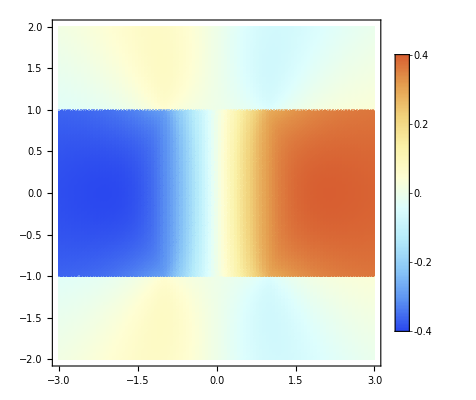

```mathematica
toplot =SYY2d;
DensityPlot[ReplaceAll[toplot,{fx->1,μ->1,ν->0.25,a->1,b->1}],{xo,-3,3},{yo,-2,2},PlotLegends->Automatic,ColorFunction->"LightTemperatureMap",PlotPoints->100]
```